In the Excel document, I copy/paste steam table data from online (which can be messy so I clean it up and get rid of what I don’t want) onto one sheet then take two columns from that at a time to put into new sheets which is what I’ll import. 

Use Import to get the lists of data. I do it sheet-by-sheet. So for the Excel document saturated steam tables we want to import the list on the second sheet (hL(P)) and on the third sheet (hV(P)). Just write the file path like how I did below for the path on my computer, followed by {"Data",#} where # is the sheet number in Excel.

```mathematica
Import["C:\\Users\\Rachael\\Dropbox\\Spring 15 simulations\\Rankine\\saturated steam tables.xlsx",{"Data",2}]
```

{{P (Mpa),hL (kJ/kg)},{0.001,29.3},{0.0012,40.6},{0.0014,50.3},{0.0016,58.8},{0.0018,66.5},{0.002,73.4},{0.003,101.},{0.004,121.4},{0.006,151.5},{0.008,173.8},{0.01,191.8},{0.012,206.9},{0.014,220.},{0.016,231.6},{0.018,242.},{0.02,251.4},{0.03,289.3},{0.04,317.6},{0.06,359.9},{0.08,391.7},{0.1,417.5},{0.12,439.4},{0.14,458.4},{0.16,475.4},{0.18,490.7},{0.2,504.7},{0.3,561.4},{0.4,604.7},{0.6,670.4},{0.8,720.9},{1.,762.5},{1.2,798.3},{1.4,830.},{1.6,858.5},{1.8,884.5},{2.,908.5},{3.,1008.3},{4.,1087.5},{6.,1213.9},{8.,1317.3},{10.,1408.1},{12.,1491.5},{14.,1571.},{16.,1649.7},{18.,1732.1},{20.,1827.2}}

It takes a second to evaluate but one it has, copy/paste the output into whichever notebook you are making your demo in. I import my data into this notebook and copy/paste it to another to keep everything neat. It has to be copy/pasted though because once you submit it, no one can access the data in the list because you’re the only one with the file it came from. Either delete or comment out any text, like {P (Mpa), hL (kJ/kg)}, because thats’s clearly not a data point. If you need to make the list a function, wrap it in Interpolation[ ] otherwise you don’t need it.

```mathematica
HL=Interpolation[
{(*{P (Mpa),hL (kJ/kg)},*){0.001,29.3},{0.0012,40.6},{0.0014,50.3},{0.0016,58.8},{0.0018,66.5},{0.002,73.4},{0.003,101.},{0.004,121.4},{0.006,151.5},{0.008,173.8},{0.01,191.8},{0.012,206.9},{0.014000000000000002,220.},{0.016,231.6},{0.018,242.},{0.02,251.4},{0.03,289.3},{0.04,317.6},{0.06,359.9},{0.08,391.7},{0.1,417.5},{0.12,439.4},{0.14,458.4},{0.16,475.4},{0.18,490.7},{0.2,504.7},{0.3,561.4},{0.4,604.7},{0.6,670.4},{0.8,720.9},{1.,762.5},{1.2,798.3},{1.4,830.},{1.6,858.5},{1.8,884.5},{2.,908.5},{3.,1008.3},{4.,1087.5},{6.,1213.9},{8.,1317.3},{10.,1408.1},{12.,1491.5},{14.,1571.},{16.,1649.7},{18.,1732.1},{20.,1827.2}}
];
```

Now I can get the saturated liquid enthalpy at any pressure between 0.001 and 20 MPa or plot pressure vs. enthalpy.

```mathematica
HL[1.92]
```

899.108

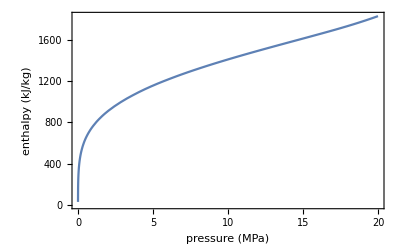

```mathematica
Plot[HL[pressure],{pressure,0.001,20},Frame->True,FrameLabel->{"pressure (MPa)","enthalpy (kJ/kg)"}]
```